```mathematica
gamma[r_,R_]:=(1-3/4*r/R+1/16*(r/R)^3)
```

```mathematica
Integrate[gamma[r,R]*2 π BesselJ[0,Q r]*r,{r,0,2*R},Assumptions->Q>0&&R>0]
```

1/(8 Q^4 R^2)3 π (4 Q R (2 Q R BesselJ[0,2 Q R]-3 BesselJ[1,2 Q R])+π (3+4 Q^2 R^2) (BesselJ[1,2 Q R] StruveH[0,2 Q R]-BesselJ[0,2 Q R] StruveH[1,2 Q R]))

```mathematica
FunctionExpand[%]
```

(3 BesselJ[1,2 Q R] (-12 π Q R+3 π^2 StruveH[0,2 Q R]+4 π^2 Q^2 R^2 StruveH[0,2 Q R]))/(8 Q^4 R^2)-(3 BesselJ[0,2 Q R] (-8 π Q^2 R^2+3 π^2 StruveH[1,2 Q R]+4 π^2 Q^2 R^2 StruveH[1,2 Q R]))/(8 Q^4 R^2)

```mathematica
FullSimplify[ReplaceAll[2*Integrate[4/3*Pi*R^3eta^2*gamma[r,R]*r/Sqrt[r^2-z^2],{r,z,2*R}, Assumptions->z>0&&z<2*R],z->xi*2*R],Assumptions->R>0&&xi<2*R]
```

eta^2 π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])

```mathematica
Integrate[gamma[r,R],{r,0,2*R}]
```

(3 R)/4

```mathematica
GzSphere:=Integrate[gamma[r,R]4*Pi*r^2,{r,0,2*R}]*2*Integrate[gamma[r,R]*r/Sqrt[r^2-z^2],{r,z,2*R}, Assumptions->z>0&&z<2*R]
```

```mathematica
GzSphere
```

1/48 π (6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))])

```mathematica
Limit[1/48 π (6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))]),z->0]
```

2 π R^3 √(R^2)

```mathematica
FullSimplify[ReplaceAll[GzSphere,z->xi*2*R],Assumptions->R>0&&xi<2*R]
```

π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])

```mathematica
Simplify[ReplaceAll[GzSphere,z->xi*2*R],Assumptions->x>0&&R>0]
```

π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])

```mathematica
ISphere[Q_,R_]:=(4/3*Pi*R^3*3(Sin[Q*R]-Q*R*Cos[Q*R])/(Q*R)^3)^2
```

```mathematica
Integrate[(lambda/(2*Pi))^2ISphere[Q,R]*2*Pi*Q,{Q,0,Infinity},Assumptions->R>0]
```

2 lambda^2 π R^4

```mathematica
FullSimplify[Integrate[gamma[r,R]*Sin[Q*r]/(Q*r)*4*Pi*r^2*eta^2*(4/3*Pi*R^3),{r,0,2*R}]]
```

(16 eta^2 π^2 (-Q R Cos[Q R]+Sin[Q R])^2)/Q^6

```mathematica
FullSimplify[Integrate[Exp[-r/xi]*4*Pi*r^2,{r,0,Infinity}],Assumptions->xi>0&&Q>0]
```

8 π xi^3

```mathematica
FullSimplify[Integrate[Exp[-r/xi]*8 π xi^3/1*Sin[Q*r]/(Q*r)*4*Pi*r^2,{r,0,Infinity}],Assumptions->xi>0&&Q>0]
```

(64 π^2 xi^6)/((1+Q^2 xi^2)^2)

```mathematica
Integrate[2*Exp[-r/xi]*r/Sqrt[r^2-z^2]*8 π xi^3,{r,z,Infinity}, Assumptions->z>0&&xi>0]
```

16 π xi^3 z BesselK[1,z/xi]

```mathematica
Integrate[Exp[-r/xi]/r*4*Pi*r^2,{r,0,Infinity},Assumptions->xi>0]
```

4 π xi^2

```mathematica
Integrate[gamma[r,R]*4*Pi*r^2,{r,0,2*R}]
```

(4 π R^3)/3

```mathematica
FullSimplify[Normal[Series[u*BesselK[1,u],{u,0,3},Assumptions->u>0]],Assumptions->u>0]
```

1+1/4 u^2 (-1+2 EulerGamma+Log[u^2/4])

```mathematica
Integrate[Exp[-r/xi]*4*Pi*r^2,{r,0,Infinity},Assumptions->xi>0]
```

8 π xi^3

```mathematica
Simplify[Limit[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H] /(Gamma[2+H]/((H+H^2) Gamma[H])),r->0,Assumptions->a>0 && H>0]]
```

1

```mathematica
Integrate[1/(Gamma[2+H]/((H+H^2) Gamma[H]))*BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*4*pi*r^2,{r,0,Infinity}, Assumptions->z>0&&a>0&&H>-2]
```

(8 a^3 pi √π Gamma[3/2+H])/Gamma[H]

```mathematica
(8 a^3 pi √π Gamma[3/2+1/2])/Gamma[1/2]
```

8 a^3 pi

```mathematica
Integrate[1/((8 a^3 pi √π Gamma[3/2+H])/Gamma[H])/(Gamma[2+H]/((H+H^2) Gamma[H]))*BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*4*pi*r^2*Sin[Q*r]/(Q*r),{r,0,Infinity}, Assumptions->Q>0&&z>0&&a>0&&H>-1/2]
```

(1+a^2 Q^2)^(-3/2-H)

```mathematica
FullSimplify[Gamma[2+H]/((H+H^2) Gamma[H])]
```

1

```mathematica
FullSimplify[Limit[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H],r->0,Assumptions->H>0&&a>0]]
```

1

```mathematica
FullSimplify[2*Integrate[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*r/Sqrt[r^2-z^2],{r,z,Infinity}, Assumptions->z>0&&a>0&&H>-2]]
```

(2^(3/2-H) √π (z/a)^H √(a z) BesselK[1/2+H,z/a])/Gamma[H]

```mathematica
GzDABH[z_,a_,H_]:=(2^(3/2-H) √π (z/a)^H √(a z) BesselK[1/2+H,z/a])/Gamma[H]
```

```mathematica
Limit[GzDABH[z,a,H],z->0,Assumptions->a>0&&H>0]
```

(2 a √π Gamma[1/2+H])/Gamma[H]

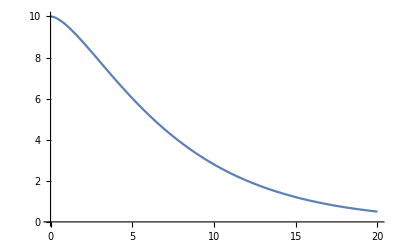

```mathematica
Plot[GzDABH[z,5,1/2],{z,0,20}]
```

```mathematica
FullSimplify[(2^(-5/2-H) (z/u)^(-5/2-H) z^(1/2+H) BesselK[1/2+H,z/(z/u)])/(π Gamma[3/2+H]),Assumptions->H>0&&u>0&&z>0]
```

(2^(-5/2-H) u^(5/2+H) BesselK[1/2+H,u])/(π z^2 Gamma[3/2+H])

```mathematica
FunctionExpand[Normal[Assuming[H>0&&a>0,Series[(2^(-5/2-H) u^(5/2+H) BesselK[1/2+H,u])/(π z^2 Gamma[3/2+H]),{u,0,3}]]]]
```

u^2/(4 (1+2 H) π z^2)-u^4/(8 (-1+2 H) (1+2 H) π z^2)-(2^(-6-2 H) u^(5+2 H) Gamma[-3/2-H])/(π z^2 Gamma[3/2+H])+(2^(-4-2 H) u^(3+2 H) Gamma[-1/2-H])/(π z^2 Gamma[3/2+H])

```mathematica
Assuming[H>0,Limit[(u/2)^(1/2+H)*BesselK[1/2+H,u],u->0]]
```

1/2 Gamma[1/2+H]

```mathematica
Integrate[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]/((8 a^3 π^(3/2) Gamma[3/2+H])/Gamma[H])*Sin[Q*r]/(Q*r)*4*Pi*r^2,{r,0,Infinity}, Assumptions->Q>0&&a>0&&H>-3/2]
```

(1+a^2 Q^2)^(-3/2-H)

```mathematica
FullSimplify[Integrate[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*((8 a^3 π^(3/2) Gamma[3/2+H])/Gamma[H])*4*Pi*r^2,{r,0,Infinity}, Assumptions->Q>0&&a>0&&H>-3]]
```

(64 a^6 π^3 Gamma[3/2+H]^2)/Gamma[H]^2

```mathematica
2*Pi*Integrate[1/(a^2+2*b*Q^2+Q^4)BesselJ[0,Q*z]*Q,{Q,0,Infinity}]
```

2 ∫_0^∞ (Q BesselJ[0,Q z])/(a^2+2 b Q^2+Q^4)ⅆQ

```mathematica
2*Integrate[Exp[-r/xi]*Sin[k*r]/(k*r)*r/Sqrt[r^2-z^2],{r,z,Infinity}, Assumptions->xi>0&&k>0&&z>0]
```

2 Integrate[(ⅇ^(-r/xi) Sin[k r])/(k √(r^2-z^2)),{r,z,∞},Assumptions→xi>0&&k>0&&z>0]

```mathematica
Integrate[Exp[-r/xi]*Sin[k*r]/(k*r)*Sin[Q*r]/(Q*r)*4*Pi*r^2,{r,0,Infinity}, Assumptions->xi>0&&k>0&&z>0&&Q>0]
```

(8 π xi^3)/(1+2 (k^2+Q^2) xi^2+(k^2-Q^2)^2 xi^4)

```mathematica
2*Pi*Integrate[(8 π xi^3)/(1+2 (k^2+Q^2) xi^2+(k^2-Q^2)^2 xi^4)*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->xi>0&&k>0&&z>0]
```

1/k 2 ⅈ π^2 (BesselJ[0,((-ⅈ+k xi) z)/xi] (Log[-(4 xi)/(-ⅈ+k xi)]+Log[xi/(-ⅈ+k xi)]-2 Log[z])-BesselJ[0,((ⅈ+k xi) z)/xi] (Log[-(4 xi)/(ⅈ+k xi)]+Log[xi/(ⅈ+k xi)]-2 Log[z])-2 Hypergeometric0F1Regularized^(1,0)[1,-1/4 (k-ⅈ/xi)^2 z^2]+2 Hypergeometric0F1Regularized^(1,0)[1,-1/4 (k+ⅈ/xi)^2 z^2])

```mathematica
FunctionExpand[%2,Assumptions->xi>0&&k>0&&z>0]
```

(2 ⅈ π^2 BesselJ[0,((-ⅈ+k xi) z)/xi] (-ⅈ π+Log[4]+2 (Log[xi]+Log[1/(-ⅈ+k xi)])-2 Log[z]))/k-(2 ⅈ π^2 BesselJ[0,((ⅈ+k xi) z)/xi] (-ⅈ π+2 Log[xi]+Log[-4/(ⅈ+k xi)]+Log[-1/(ⅈ+k xi)]-2 Log[z]))/k-(4 ⅈ π^2 Hypergeometric0F1Regularized^(1,0)[1,-1/4 (k-ⅈ/xi)^2 z^2])/k+(4 ⅈ π^2 Hypergeometric0F1Regularized^(1,0)[1,-1/4 (k+ⅈ/xi)^2 z^2])/k

```mathematica
2*Pi*Series[Integrate[(Q*L)^(2*n+1)*(-1)^n/((2*n+1)*(2*n+1)!)/(Q*L)BesselJ[0,Q*z]*Q,Q,Assumptions->L>0&&z>0&&n>0&&n is Integers],{n,0,Infinity}]
```

Series::serlim: Series order specification ∞ is not a machine-sized integer.

2 π Series[((-1)^n Q^2 (L Q)^(2 n) Gamma[1+n] HypergeometricPFQRegularized[{1+n},{1,2+n},-1/4 Q^2 z^2])/(2 (1+2 n) (1+2 n)!),{n,0,∞}]

```mathematica
2*Pi*Integrate[SinIntegral[Q*L]/(Q*L)BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->L>0&&z>0]
```

(π^(3/2) (Piecewise[{{0, L≤z}, {(2 ArcCos[z/L])/(√π), True}}]))/(L z)

```mathematica
2*Pi*Integrate[(Sin[Q*L/2]/(Q*L/2))^2BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->L>0&&z>0]
```

(2 π^(3/2) (Piecewise[{{0, L≤z}, {(2 Log[(L+√(L^2-z^2))/z])/(√π), True}}]))/L^2

```mathematica
2*Pi*Integrate[(1-BesselJ[1,2*Q*R]/(Q*R))/(Q*R)^2*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->R>0&&z>0]
```

2 π Integrate[(BesselJ[0,Q z] (1-BesselJ[1,2 Q R]/(Q R)))/(Q R^2),{Q,0,∞},Assumptions→R>0&&z>0]

```mathematica
Normal[Series[(1-BesselJ[1,2*Q*R]/(R*Q))/(R*Q)^2,{Q,Infinity,2},Assumptions->R>0]]
```

1/(Q^2 R^2)+((1/Q)^(7/2) Cos[π/4+2 Q R])/(√π R^(7/2))-(3 (1/Q)^(9/2) Sin[π/4+2 Q R])/(16 √π R^(9/2))

```mathematica
Assuming[L>0&&z>0&&R>0&&R<L,Integrate[(Sin[Q*L/2]/(Q*L/2))^2*(1-0*BesselJ[1,2*Q*R]/(R*Q))/(1+(R*Q)^2)*BesselJ[0,Q*z]*Q,{Q,0,Infinity}]]
```

∫_0^∞ (4 BesselJ[0,Q z] Sin[(L Q)/2]^2)/(L^2 Q (1+Q^2 R^2))ⅆQ

```mathematica
Assuming[L>0&&z>0&&Qmax>0,Integrate[2*SinIntegral[Q*L]/(Q*L)Exp[-a^2*Q^2]*BesselJ[0,Q*z]*Q,{Q,0,Infinity}]]
```

∫_0^∞ (2 ⅇ^(-a^2 Q^2) BesselJ[0,Q z] SinIntegral[L Q])/L ⅆQ

```mathematica
2*Pi*Integrate[2*SinIntegral[Q*L]/(Q*L)*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->L>0&&z>0&&Qmax>0]+2*Pi*Integrate[(Sin[Q*L/2]/(Q*L/2))^2*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->L>0&&z>0&&Qmax>0]
```

2 π Integrate[(4 BesselJ[0,Q z] Sin[(L Q)/2]^2)/(L^2 Q),{Q,0,Qmax},Assumptions→L>0&&z>0&&Qmax>0]+(2 π^(3/2) (Piecewise[{{0, L≤z}, {(2 ArcCos[z/L])/(√π), True}}]))/(L z)

```mathematica
FullSimplify[ComplexExpand[%]]
```

Piecewise[{{0, L≤z}, {(4 π (L ArcCos[z/L]+z Log[(L+√(L^2-z^2))/z]))/(L^2 z), True}}]

```mathematica
Limit[(4 π (L ArcCos[z/L]+z Log[(L+√(L^2-z^2))/z]))/(L^2 z),z->0,Assumptions->L>0]
```

∞

```mathematica
CForm[(4 π (L ArcCos[z/L]+z Log[(L+√(L^2-z^2))/z]))/(L^2 z)]
```

```mathematica
(4*Pi*(L*ArcCos(z/L) + z*Log((L -+ Sqrt(Power(L,2) - Power(z,2)))/z)))/
   (Power(L,2)*z)
```

```mathematica
2*Pi*Integrate[(BesselJ[1,Q*R]/(Q*R))^2*SinIntegral[Q*L]/(Q*L)*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->L>0&&z>0&& R>0]
```

2 π Integrate[(BesselJ[0,Q z] BesselJ[1,Q R]^2 SinIntegral[L Q])/(L Q^2 R^2),{Q,0,∞},Assumptions→L>0&&z>0&&R>0]

```mathematica
2*Pi*Integrate[(Exp[-(Q^2*Rg^2)]+(Q^2*Rg^2)-1)/(Q^2*Rg^2)^2*BesselJ[0,Q*z]*Q,{Q,0,Qmax},Assumptions->Rg>0&&z==0]
```

(π (1/Qmax^2-(ⅇ^(-Qmax^2 Rg^2))/Qmax^2-Rg^2+EulerGamma Rg^2+Rg^2 Gamma[0,Qmax^2 Rg^2]+Rg^2 Log[Qmax^2]+2 Rg^2 Log[Rg]))/Rg^4

```mathematica
2*Pi*Integrate[(Exp[-(Q^2*Rg^2)]+(Q^2*Rg^2)-1)/(Q^2*Rg^2)^2*BesselJ[0,Q*z]*Q,{Q,0,Qmax},Assumptions->Rg>0&&z>0]
```

2 π Integrate[((-1+ⅇ^(-Q^2 Rg^2)+Q^2 Rg^2) BesselJ[0,Q z])/(Q^3 Rg^4),{Q,0,Qmax},Assumptions→Rg>0&&z>0]

```mathematica
2*Pi*Integrate[(Exp[-(Q^2*Rg^2*(2*nu+1)*(2*nu+2))/6*x^(2*nu)])*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->Rg>0&&nu>0&&z>0&&x>0]
```

(3 ⅇ^(-(3 x^(-2 nu) z^2)/(4 (1+nu) (1+2 nu) Rg^2)) π x^(-2 nu))/((1+nu) (1+2 nu) Rg^2)

```mathematica
Integrate[(3 ⅇ^(-(3 x^(-2 nu) z^2)/(4 (1+nu) (1+2 nu) Rg^2)) π x^(-2 nu))/((1+nu) (1+2 nu) Rg^2)*2*(1-x),{x,0,1},Assumptions->Rg>0&&nu>0&&z>0]
```

(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(nu (1+nu) (1+2 nu) Rg^2)

```mathematica
FunctionExpand[(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(nu (1+nu) (1+2 nu) Rg^2),Assumptions->nu>0&&Rg>0]
```

-(3^(1/nu) 4^(1-1/nu) π (z^2/((1+3 nu+2 nu^2) Rg^2))^(-1+1/nu) Gamma[1-1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)])/(nu (1+nu) (1+2 nu) Rg^2)+(3^(1/2/nu) 4^(1-1/(2 nu)) π (z^2/((1+3 nu+2 nu^2) Rg^2))^(-1+1/(2 nu)) Gamma[1-1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)])/(nu (1+nu) (1+2 nu) Rg^2)

```mathematica
ReplaceAll[z^2/((1+3 nu+2 nu^2) Rg^2)->w][-(3^(1/nu) 4^(1-1/nu) π (z^2/((1+3 nu+2 nu^2) Rg^2))^(-1+1/nu) Gamma[1-1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)])/(nu (1+nu) (1+2 nu) Rg^2)+(3^(1/2/nu) 4^(1-1/(2 nu)) π (z^2/((1+3 nu+2 nu^2) Rg^2))^(-1+1/(2 nu)) Gamma[1-1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)])/(nu (1+nu) (1+2 nu) Rg^2)]
```

-(3^(1/nu) 4^(1-1/nu) π w^(-1+1/nu) Gamma[1-1/nu,(3 w)/4])/(nu (1+nu) (1+2 nu) Rg^2)+(3^(1/2/nu) 4^(1-1/(2 nu)) π w^(-1+1/(2 nu)) Gamma[1-1/(2 nu),(3 w)/4])/(nu (1+nu) (1+2 nu) Rg^2)

```mathematica
FullSimplify[nu (1+nu) (1+2 nu) Rg^2*z^2/((1+3 nu+2 nu^2) Rg^2)]
```

nu z^2

```mathematica
Simplify[Factor[FunctionExpand[(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(nu (1+nu) (1+2 nu) Rg^2)]]]
```

1/(nu z^2)(2^(2-1/nu) 3^(1/2/nu) π (z^2/((1+3 nu+2 nu^2) Rg^2))^(1/2/nu) Gamma[1-1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-2^(2-2/nu) 3^(1/nu) π (z^2/((1+3 nu+2 nu^2) Rg^2))^(1/nu) Gamma[(-1+nu)/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)])

```mathematica
ExpIntegralE[3.2,0.1]
```

0.382506+4.85472×10^-17 ⅈ

```mathematica
Limit[(3 π ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)])/(2 nu (1+nu) (1+2 nu) Rg^2),z->0]
```

```mathematica
FullSimplify[Limit[(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(2 nu (1+nu) (1+2 nu) Rg^2)*2,z->0,Assumptions->Rg>0&&nu>0]]
```

Limit[(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(nu (1+nu) (1+2 nu) Rg^2),z→0,Assumptions→Rg>0&&nu>0]

```mathematica
Limit[(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(2 nu (1+nu) (1+2 nu) Rg^2)*2,z->0,Assumptions->Rg>0&&nu>0&&nu<1/2]
```

```mathematica
TeXForm[(3 π)/((1-5 nu^2+4 nu^4) Rg^2)]
```

\frac{3 \pi }{\left(4 \nu ^4-5 \nu ^2+1\right) \text{Rg}^2}

```mathematica
FullSimplify[Normal[Series[(3 π (ExpIntegralE[1/(2 nu),(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]-ExpIntegralE[1/nu,(3 z^2)/(4 (1+3 nu+2 nu^2) Rg^2)]))/(2 nu (1+nu) (1+2 nu) Rg^2)*2,{z,0,3},Assumptions->Rg>0&&nu>0&&z>0]]]
```

π (3/((1-5 nu^2+4 nu^4) Rg^2)-(9 z^2)/(4 (1+3 nu+2 nu^2)^2 (1-6 nu+8 nu^2) Rg^4)+(2^((-2+nu)/nu) (1/3+nu+(2 nu^2)/3)^(-1/nu) (Rg/z)^(-2/nu) (2 Gamma[-1/nu]-2^(1/nu) (1/3+nu+(2 nu^2)/3)^(1/2/nu) (Rg/z)^(1/nu) Gamma[-1/(2 nu)]))/(nu^2 z^2))

```mathematica
2*Pi*Integrate[((64 π^2 xi^6)/((1+Q^2 xi^2)^2))*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->xi>0&&z>0]
```

64 π^3 xi^3 z BesselK[1,z/xi]

```mathematica
2*Pi*Integrate[(IQsphere[Q,R])*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->xi>0&&z>0]
```

```mathematica
2 π Integrate[Q BesselJ[0,Q z] ISphere[Q,R],{Q,0,∞},Assumptions->R>0&&z>0]
```

2 π Integrate[(16 π^2 BesselJ[0,Q z] (-Q R Cos[Q R]+Sin[Q R])^2)/Q^5,{Q,0,∞},Assumptions→R>0&&z>0]

```mathematica
ISphere[Q,R]
```

(16 π^2 (-Q R Cos[Q R]+Sin[Q R])^2)/Q^6

```mathematica
Integrate[Cos[Q*r*Cos[a]],{a,-Pi,Pi},Assumptions->r>0&&Q>0]
```

2 π BesselJ[0,Q r]

```mathematica
Integrate[Cos[Q*r],{a,-Pi,Pi},Assumptions->r>0&&Q>0]
```

2 π Cos[Q r]